## Marginally bound geodesics

### Prove that P(r) is a 3rd order polynomial

```mathematica
Pr=(Eps(r^2+a^2)-a*L)^2-Delt(Q+(L-a*Eps)^2+mu*r^2);
```

```mathematica
Collect[Pr/.Delt->r^2-Rs*r+a^2/.mu->Eps^2, r, Simplify]
```

-a^2 Q+(-L^2-Q) r^2+((-a Eps+L)^2+Q) r Rs+Eps^2 r^3 Rs

```mathematica
Pr2 = -a^2 Q+(-L^2-Q) r^2+((-a Eps+L)^2+Q) r Rs+Eps^2 r^3 Rs;
RsPlus = Rs/2+Rs/2*Sqrt[1-(4 a^2)/Rs^2];
```

### Study the equatorial limit Q = 0

#### Get the P(r) for Q=0

```mathematica
PrEquat = Pr2/.Q->0/.r->r0
```

-L^2 r0^2+(-a Eps+L)^2 r0 Rs+Eps^2 r0^3 Rs

#### Solve P(r) = 0

```mathematica
EquatSol=Solve[{PrEquat==0}, r0]/.Rule[a_,b_]->b/.Rs->2M//Expand//Simplify
```

{{0},{(L^2-√(L^4-16 a^2 Eps^4 M^2+32 a Eps^3 L M^2-16 Eps^2 L^2 M^2))/(4 Eps^2 M)},{(L^2+√(L^4-16 a^2 Eps^4 M^2+32 a Eps^3 L M^2-16 Eps^2 L^2 M^2))/(4 Eps^2 M)}}

#### Equate r2=r3 and solve for a

Note how the equation r_2=r_3 is of order 4 in L while order 2 in a.

```mathematica
rootsL= Solve[{EquatSol[[2]]==EquatSol[[3]]}, a, Reals]/.Rule[a_,b_]->b
```

{{ConditionalExpression[(-L^2+4 Eps L M)/(4 Eps^2 M), M>0||M<0]},{ConditionalExpression[(L^2+4 Eps L M)/(4 Eps^2 M), M>0||M<0]}}

#### Plug a back to the equation P(r)=0 and solve for L

```mathematica
Solve[PrEquat==0/.a->(L^2+4 Eps L M)/(4 Eps^2 M), L]/.Rs->2M//FullSimplify
Solve[PrEquat==0/.a->(-L^2+4 Eps L M)/(4 Eps^2 M), L]/.Rs->2M//FullSimplify
```

{{L→-2 √(Eps^2 M r0)},{L→2 √(Eps^2 M r0)},{L→-2 √(Eps^2 M r0)},{L→2 √(Eps^2 M r0)}}

{{L→-2 √(Eps^2 M r0)},{L→2 √(Eps^2 M r0)},{L→-2 √(Eps^2 M r0)},{L→2 √(Eps^2 M r0)}}

```mathematica
EquatSol[[3]]/.a->(-L^2+4 Eps L M)/(4 Eps^2 M)//Expand//FullSimplify
```

{L^2/(4 Eps^2 M)}

#### Plug L to P(r) and solve again for r0

We require r_0>r_+. And we get two solutions. One for positive angular momentum and one for negative angular momentum.

```mathematica
Rs=2M
```

2 M

```mathematica
Solve[{PrEquat==0/.L->2 √(Eps^2 M r0), r0>RsPlus}, r0]/.Rule[a_,b_]->b//Expand//Simplify
Solve[{PrEquat==0/.L->-2 √(Eps^2 M r0), r0>RsPlus}, r0]/.Rule[a_,b_]->b/.Rs->2M//Expand//Simplify
```

{{ConditionalExpression[0, a≠0&&√(a^2)+M≤0]},{ConditionalExpression[-a+2 (M+√(M (-a+M))), ]},{ConditionalExpression[a+2 (M+√(M (a+M))), ]}}

{{ConditionalExpression[0, a≠0&&√(a^2)+M≤0]},{ConditionalExpression[-a+2 (M+√(M (-a+M))), ]},{ConditionalExpression[a+2 (M+√(M (a+M))), ]}}

### Time for some plots!

1.6

0.4

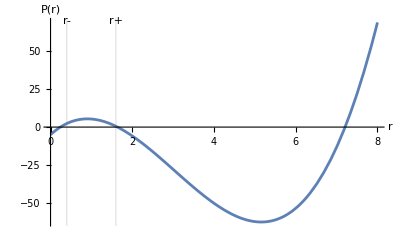

```mathematica
a=0.8;
Eps=0.94;
L=2.86192;
Q=7.8688;
M=1;
RsPlus = Rs/2+Rs/2*Sqrt[1-(4 a^2)/Rs^2]
RsMinus =  Rs/2-Rs/2*Sqrt[1-(4 a^2)/Rs^2]
Case2 =Plot[Pr2,{r,0,8},GridLines->{{RsMinus,RsPlus},{}},AxesLabel->{HoldForm[r],HoldForm[P[r]]},PlotLegends->Row[{" a = ",a,"\n Eps = ",Eps,"\n L = ",L,"\n Q = ",Q,"\n M = ",M}], Epilog->{Text["r-",{RsMinus,70},{-2,0}],Text["r+",{RsPlus,70},{-2,0}]} ]
```

```mathematica
SetDirectory[NotebookDirectory[]]
Export["case2_a.png",Case2, ImageResolution->500]
```

/home/kpapad/Documents/GraduateStuff/BHGW/Homeworks

case2_a.png

1.66144

0.338562

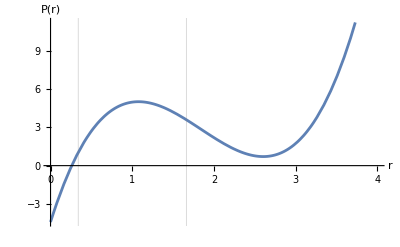

```mathematica
a=0.75;
Eps=1.101;
L=2.34665;
Q=7.8688;
M=1;
RsPlus =  Rs/2+Rs/2*Sqrt[1-(4 a^2)/Rs^2]
RsMinus =  Rs/2-Rs/2*Sqrt[1-(4 a^2)/Rs^2]
Case3 =Plot[Pr2,{r,0,4},GridLines->{{RsMinus,RsPlus},{}},AxesLabel->{HoldForm[r],HoldForm[P[r]]},PlotLegends->Row[{" a = ",a,"\n Eps = ",Eps,"\n L = ",L,"\n Q = ",Q,"\n M = ",M}], Epilog->{Text["r-",{RsMinus,155},{-2,0}],Text["r+",{RsPlus,155},{-2,0}]} ]
```

```mathematica
Export["case1.png",Case2, ImageResolution->500]
```

case1.png

```mathematica
Clear[a,Eps,L,Q,M, Rs, RsPlus, RsMinus]
```

## Kerry Metric

### Define auxiliary terms

```mathematica
Clear[Delt, Sigm, a, r]
```

```mathematica
Sigm = r^2+a^2 Cos[u]^2;
Delt = r^2-Rs*r+a^2;
```

### Define the metric components

```mathematica
g[tt] = -(1-(Rs*r)/Sigm);
g[rr]=Sigm/Delt;
g[uu]=Sigm; (*u stands for theta*)
g[vv]=(((r^2+a^2)^2-Delt*a^2*Sin[u]^2)/Sigm)Sin[u]^2; (*v stands for phi*)
g[tv] = -(2*a*Rs*r)/Sigm Sin[u]^2;
```

#### Expand each component around a=0

```mathematica
Series[g[tt], {a,0,1}]
```

(-1+Rs/r)+O[a]^2

```mathematica
Series[g[rr], {a,0, 1}]
```

r/(r-Rs)+O[a]^2

```mathematica
Series[g[uu], {a, 0 ,1}]
```

r^2+O[a]^2

```mathematica
Series[g[vv], {a, 0, 1}]
```

r^2 Sin[u]^2+O[a]^2

```mathematica
Series[g[tv],{a,0,1}]
```

-(2 (Rs Sin[u]^2) a)/r+O[a]^2

Compare this to the schwarzchild metric to find that h_tϕ=(-2Rs sin^2 θ)/r. Note that all the rest of the components of h are 0. Thus, in  ∇_a h_μα the only non zero term is ∇^α h_tα= ∇^t h_tt +∇^r h_tr +∇^ϕ h_tϕ +∇^θ h_tθ =∇^ϕ h_tϕ=0 , since the g_tϕ tern doesn’t depend on ϕ. Therefore we have  ∇^α h_μα = 0. On the other hand the trace h=(h_αβ(g^schw))^αβ=0, since h is off diagonal and g^schw is diagonal. Therefore, ∇_μ h = 0.  ∴  ∇^α h_μα = 1/2∇_μ h =0.

### Schwarzschild metric around M=M_0

```mathematica
Rs = 2M;
```

```mathematica
g[tt]
```

-1+(2 M r)/(r^2+a^2 Cos[u]^2)

```mathematica
gs[tt] = -(1-Rs/r);
gs[rr] = 1/(1-Rs/r);
gs[oo] = r^2; (*o stands of omega*)
```

```mathematica
Series[gs[rr], {M, M0, 1}]
```

1/(1-(2 M0)/r)+(2 r (M-M0))/(2 M0-r)^2+O[M-M0]^2

```mathematica
Series[gs[tt], {M, M0, 1}]
```

(-1+(2 M0)/r)+(2 (M-M0))/r+O[M-M0]^2

### Calculate the covariant derivative of h_μν

#### First calculate the Christoffel symbols for the Schwarzschild metric

```mathematica
gsch = {{gs[tt], 0, 0 ,0}, {0, gs[rr], 0, 0}, {0, 0, r^2, 0}, {0, 0, 0, r^2 Sin[u]^2}}; (*u stands for theta*)
Gsch = Table[gsch[[ii]][[jj]], {ii, 1, 4}, {jj, 1, 4}]/.M->M0;
Gsch//MatrixForm
```

(-1+(2 M0)/r | 0 | 0 | 0
0 | 1/(1-(2 M0)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[u]^2)

```mathematica
Ginv = Inverse[Gsch]//Simplify;
XX = {t, r, u, v};
Ginv//MatrixForm
```

(r/(2 M0-r) | 0 | 0 | 0
0 | 1-(2 M0)/r | 0 | 0
0 | 0 | 1/r^2 | 0
0 | 0 | 0 | Csc[u]^2/r^2)

```mathematica
Christ=1/2 Table[ 
Sum[ Ginv[[mm]][[ll]](D[Gsch[[bb]][[ll]], XX[[aa]]]+D[Gsch[[aa]][[ll]], XX[[bb]]] - D[Gsch[[aa]][[bb]], XX[[ll]]]), {ll, 1, 4}],
{mm, 1, 4}, {aa, 1,4 }, {bb, 1, 4}
];
```

```mathematica
Christ//MatrixForm
```

((0
-M0/((2 M0-r) r)
0
0) | (-M0/((2 M0-r) r)
0
0
0) | (0
0
0
0) | (0
0
0
0)
((M0 (1-(2 M0)/r))/r^2
0
0
0) | (0
-M0/((1-(2 M0)/r) r^2)
0
0) | (0
0
-((1-(2 M0)/r) r)
0) | (0
0
0
-((1-(2 M0)/r) r Sin[u]^2))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
-Cos[u] Sin[u])
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
Cot[u]) | (0
1/r
Cot[u]
0))

#### Calculate the covariant derivative

```mathematica
hm1 = {{2/r, 0, 0, 0}, {0,(2 r)/(2 M0-r)^2, 0, 0 }, {0, 0, 0,0}, {0,0,0,0}};
hm = Table[hm1[[ii]][[jj]], {ii,1,4},{jj,1,4}];
hm//MatrixForm
```

(2/r | 0 | 0 | 0
0 | (2 r)/(2 M0-r)^2 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
CovDevH = Table[
D[hm[[a]][[b]],XX[[c]]]- Sum[Christ[[d]][[c]][[a]]*hm[[d]][[b]], {d, 1, 4} ] - Sum[Christ[[d]][[c]][[b]]*hm[[a]][[d]], {d, 1, 4} ],
{c, 1, 4}, {a, 1, 4}, {b, 1, 4}
];
```

```mathematica
CovDevHContracted = Table[
Sum[ Ginv[[m]][[b]]*CovDevH[[m]][[a]][[b]], {m, 1, 4}, {b, 1, 4}],
{a, 1, 4}
]//Simplify
```

{0,-2/(2 M0 r-r^2),0,0}

#### Calculate the covariant derivative of the trace

```mathematica
hTrace = Sum[ hm[[a]][[b]]*Ginv[[a]][[b]], {a, 1, 4}, {b, 1, 4}]//FullSimplify
```

0

```mathematica
ScalarDerH = Table[D[hTrace, XX[[m]]], {m, 1, 4}]//FullSimplify
```

{0,0,0,0}

```mathematica
CovDevHContracted === 0.5*ScalarDerH
```

False

We see that this time h doesn’t  satisfy the Lorenz gauge condition.

```mathematica
Nm=CovDevHContracted-1/2*ScalarDerH//FullSimplify;
Nm//MatrixForm
```

(0
-2/(2 M0 r-r^2)
0
0)

### Find the gauge transformation

```mathematica
xi = {0,X2[r],0,0}; (*The gauge transformation*)
```

#### Calculate the term

```mathematica
TwoPartXi = Table[ D[ D[xi[[mm]], XX[[bb]]], XX[[aa]]], {aa, 1, 4}, {bb,1,4}, {mm, 1, 4}];
```

```mathematica
DoublePartXi = Table[ Sum[Ginv[[aa]][[bb]]*TwoPartXi[[aa]][[bb]][[mm]], {aa,1,4},{bb,1,4}], {mm, 1, 4}]
```

{0,(1-(2 M0)/r) X2''[r],0,0}

#### Calculate the term

```mathematica
PartChrist = Table[ D[Christ[[ll]][[bb]][[mm]], XX[[aa]] ], {aa,1,4},{bb,1,4},{mm,1,4},{ll,1,4}];
```

```mathematica
t1 = Table[ Sum[ PartChrist[[aa]][[bb]][[mm]][[rr]]*xi[[ll]]*Ginv[[ll]][[ee]]Gsch[[rr]][[ee]], {rr,1,4},{ll,1,4},{ee,1,4}],{aa,1,4},{bb,1,4},{mm,1,4}];
T1 = Table [Sum[ t1[[aa]][[bb]][[mm]]*Ginv[[aa]][[bb]],{aa,1,4},{bb,1,4}],{mm,1,4}]//FullSimplify
```

{0,(2 M0 (M0-r) X2[r])/((2 M0-r) r^3),0,0}

#### Calculate the term

```mathematica
t2 = Table[D[xi[[rr]] , XX[[aa]]], {aa,1,4},{rr,1,4}];
t2a = Table[ Sum[ Christ[[ll]][[bb]][[mm]]*t2[[aa]][[rr]]*Ginv[[rr]][[ee]]Gsch[[ee]][[ll]], {ll,1,4},{rr,1,4},{ee,1,4}],{bb,1,4},{mm,1,4},{aa,1,4}]//Simplify;
```

```mathematica
T2 = Table[ Sum[ t2a[[bb]][[mm]][[aa]]*Ginv[[aa]][[bb]],{aa,1,4},{bb,1,4}],{mm,1,4}]//FullSimplify
```

{0,-(M0 X2'[r])/r^2,0,0}

#### Calculate the term

```mathematica
t3 = Table[D[xi[[rr]] , XX[[mm]]], {mm,1,4},{rr,1,4}];
t3a = Table[ Sum[ Christ[[rr]][[aa]][[bb]]*t3[[ee]][[mm]]*Ginv[[ee]][[ll]]*Gsch[[ll]][[rr]], {ee,1,4},{ll,1,4},{rr,1,4}],{aa,1,4},{bb,1,4},{mm,1,4}]//Simplify;
T3 = Table[ Sum[ t3a[[aa]][[bb]][[mm]]*Ginv[[aa]][[bb]],{aa,1,4},{bb,1,4}],{mm,1,4}]//Simplify
```

{0,(2 (M0-r) X2'[r])/r^2,0,0}

#### Calculate the term

```mathematica
T4=T2
```

{0,-(M0 X2'[r])/r^2,0,0}

#### Calculate the term

```mathematica
t5=Table[Sum[Christ[[ll]][[rr]][[mm]]xi[[th]]Ginv[[th]][[zz]]Gsch[[zz]][[ll]],{th,1,4},{zz,1,4},{ll,1,4}],{rr,1,4},{mm,1,4}];
```

```mathematica
t5a= Table[Sum[ Christ[[rr]][[aa]][[bb]]t5[[dd]][[mm]]Ginv[[dd]][[ee]]Gsch[[ee]][[rr]],{rr,1,4},{dd,1,4},{ee,1,4}],{aa,1,4},{bb,1,4},{mm,1,4}];
```

```mathematica
T5=Table[Sum[t5a[[aa]][[bb]][[mm]]Ginv[[aa]][[bb]],{aa,1,4},{bb,1,4} ],{mm,1,4}]//Simplify
```

{0,(2 M0 (M0-r) X2[r])/((2 M0-r) r^3),-((2 M0-r) Cot[u] X2[r])/r^2,0}

#### Calculate the term

```mathematica
t6a= Table[Sum[ Christ[[rr]][[aa]][[mm]]t5[[dd]][[bb]]Ginv[[ee]][[dd]]Gsch[[rr]][[ee]],{rr,1,4},{dd,1,4},{ee,1,4}],{aa,1,4},{mm,1,4},{bb,1,4}];
T6=Table[Sum[t6a[[aa]][[mm]][[bb]]Ginv[[aa]][[bb]],{aa,1,4},{bb,1,4} ],{mm,1,4}]//Simplify
```

{0,(2 (2 M0-r) X2[r])/r^3,((2 M0-r) Cot[u] X2[r])/r^2,0}

#### LHS

```mathematica
lhs=DoublePartXi-T1-T2-T3-T4+T5+T6//FullSimplify
```

{0,((4 M0-2 r) X2[r]+r^2 (2 X2'[r]+(-2 M0+r) X2''[r]))/r^3,0,0}

#### RHS

```mathematica
rhs = Nm//Simplify
```

{0,-2/(2 M0 r-r^2),0,0}

#### Solve the differential equation

```mathematica
eqs=Table[ lhs[[i]]==-rhs[[i]], {i,1,4}]
```

{True,((4 M0-2 r) X2[r]+r^2 (2 X2'[r]+(-2 M0+r) X2''[r]))/r^3==2/(2 M0 r-r^2),True,True}

```mathematica
DSolve[eqs[[2]]//Simplify, X2[r], r]
```

{{X2[r]→C[1]/(2 M0 r-r^2)-(r^2 C[2])/(3 (-2 M0+r))+(4 M0^2 r+M0 r^2+r^3 Log[r]+8 M0^3 Log[-2 M0+r]-r^3 Log[-2 M0+r])/(3 M0 r (-2 M0+r))}}